# Statistical time series analysis

## University of Duisburg-Essen Faculty of Physics

Juan Camilo Henao Londono

## Brownian motion

To be done

## Stock prices

I selected the following 10 shares of the stock index S&P 500

Financials (F)

CME - CME Group Inc.

GS - Goldman Sachs Group

Consumer Discretionary (CD)

AMZN - Amazon Corp.

NKE - NIKE Inc.

Energy (E)

XOM - Exxon Mobil Corp.

CVX - Chevron Corp.

Information Technology (IT)

Microsoft Corp.

AAPL - Apple Inc.

Telecommunications services (TS)

Sprint Nextel Corp.

VZ - Verizon Communications

Load Data

```mathematica
CME = FinancialData["CME", "Jul, 1, 2009"];
GS = FinancialData["GS", "Jul, 1, 2009"];
AMZN = FinancialData["AMZN", "Jul, 1, 2009"];
NKE = FinancialData["NKE", "Jul, 1, 2009"];
XOM = FinancialData["XOM", "Jul, 1, 2009"];
CVX = FinancialData["CVX", "Jul, 1, 2009"];
MSFT = FinancialData["MSFT", "Jul, 1, 2009"];
AAPL = FinancialData["AAPL", "Jul, 1, 2009"];
S = FinancialData["S", "Jul, 1, 2009"];
VZ = FinancialData["VZ", "Jul, 1, 2009"];
```

Make a list to easily work with the shares and test if all the stocks have the same data points

```mathematica
shares = {CME, GS, AMZN, NKE, XOM, CVX, MSFT, AAPL, S, VZ};
names = {"CME", "GS", "AMZN", "NKE", "XOM", "CVX", "MSFT", "AAPL", "S", "VZ"};
```

```mathematica
dataPointsNumber =Length[#["Values"]]&/@shares;
```

Check if there is a share with different number of data points. If the list is empty, all the shares have the same amount of points

```mathematica
Position[# ≠ Commonest[dataPointsNumber][[1]] &/@ dataPointsNumber, True]
```

{}

All the stocks look like

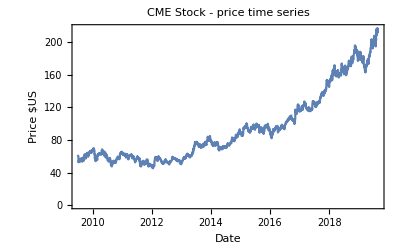
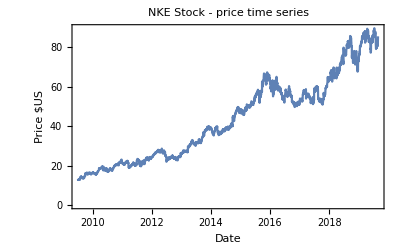
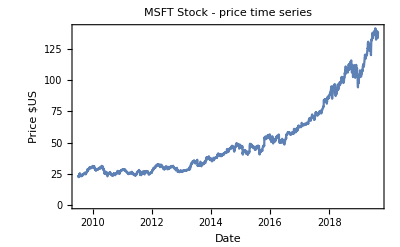
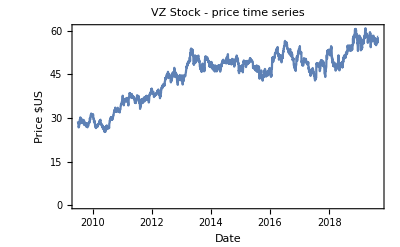
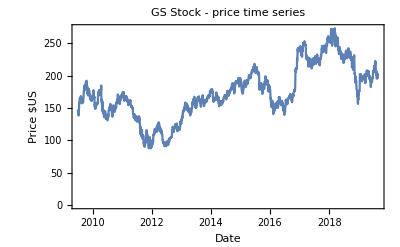
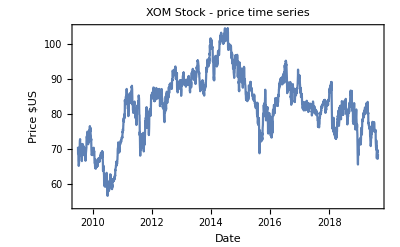
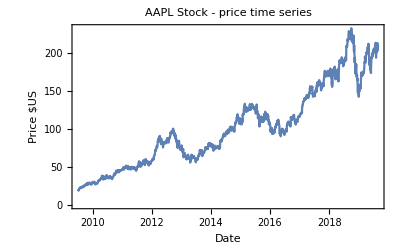
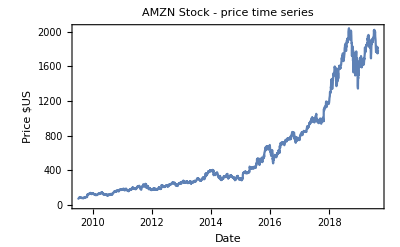
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[Table[DateListPlot[shares[[i]], PlotTheme->"Detailed", PlotLabel->StringForm["`` Stock - price time series",names[[i]]], FrameLabel->{"Date","Price $US"}],{i,10}]]
```

Returns R(τ)=(S(t+τ)-S(t))/(S(t)) with τ=1 day

```mathematica
sharesDifferences = Differences/@ shares;
sharesReturns = sharesDifferences / shares;
```

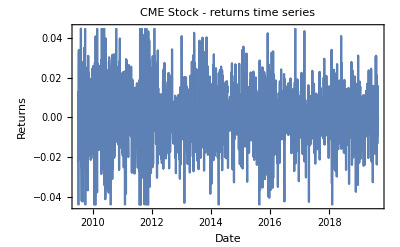
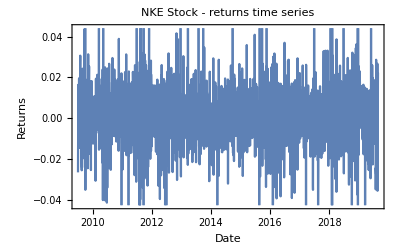
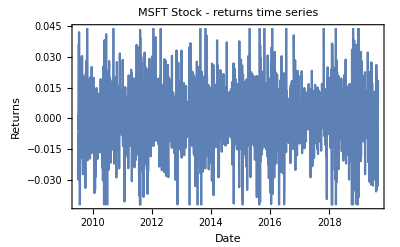
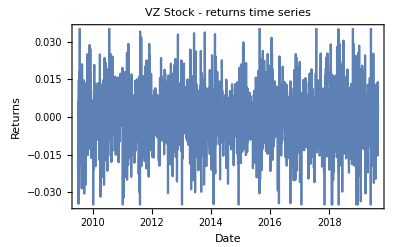
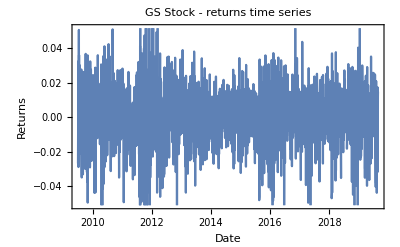
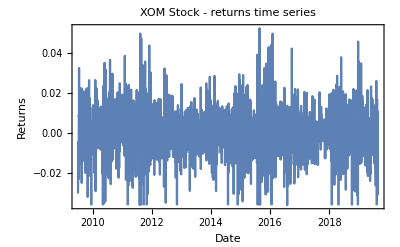
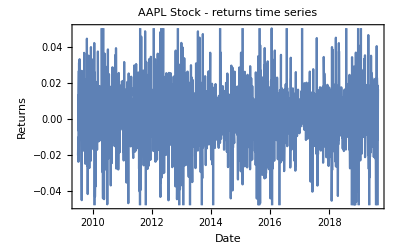
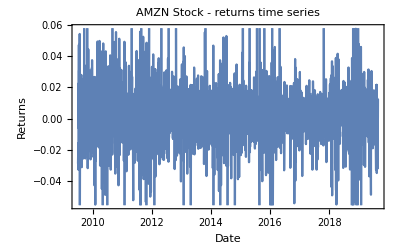
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- |

```mathematica
Multicolumn[Table[DateListPlot[sharesReturns[[i]],PlotTheme->"Detailed",PlotLabel->StringForm["`` Stock - returns time series",names[[i]]],FrameLabel->{"Date","Returns"}],{i,10}]]
```

The central moments of the returns of all ten stocks are

```mathematica
meanReturns = Mean /@ sharesReturns;
varianceReturns = Variance /@ sharesReturns;
skewnessReturns = Skewness /@ sharesReturns;
kurtosisReturns = Kurtosis /@ sharesReturns;
TableForm[{meanReturns, varianceReturns, skewnessReturns, kurtosisReturns}, TableHeadings->{{"Mean", "Variance", "Skewness", "Kurtosis"}, names}]
```

| CME | GS | AMZN | NKE | XOM | CVX | MSFT | AAPL | S | VZ
Mean | 0.00037973 $ | -0.0000128025 $ | 0.00100013 $ | 0.000620269 $ | -0.0000814584 $ | 0.000133473 $ | 0.000577471 $ | 0.00077493 $ | -0.000343844 $ | 0.000213924 $
Variance | 0.000219917 $^2/None^2 | 0.000279679 $^2/None^2 | 0.000407103 $^2/None^2 | 0.00022284 $^2/None^2 | 0.000139253 $^2/None^2 | 0.000178199 $^2/None^2 | 0.00021153 $^2/None^2 | 0.000268745 $^2/None^2 | 0.000998102 $^2/None^2 | 0.000118162 $^2/None^2
Skewness | -0.477681 | -0.645758 | 0.319198 | 0.22616 | -0.252694 | -0.276229 | -0.34468 | -0.478721 | -0.414453 | -0.194309
Kurtosis | 7.65959 | 8.3633 | 13.5012 | 10.7467 | 5.71094 | 5.43094 | 9.85755 | 8.19342 | 11.0644 | 5.25899

Normalize the return time series of each stock, subtracting the mean and dividing by the standard deviation

```mathematica
normalizedReturns=
```